# HW5 problems in Mathematica #2 - 7.2 a

{1,1,1,1,0,0,0,0}

{4,-ⅈ ((1+ⅈ)+√2),0,(1+ⅈ)-ⅈ √2,0,(1-ⅈ)+ⅈ √2,0,(1+ⅈ)+ⅈ √2}

{4.,1.-2.41421 ⅈ,0.,1.-0.414214 ⅈ,0.,1.+0.414214 ⅈ,0.,1.+2.41421 ⅈ}

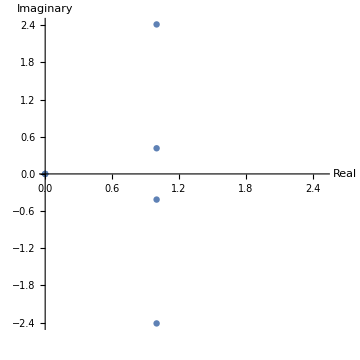

```mathematica
x1={1,1,1,1,0,0,0,0}
len=Length[x1];
k=Range[0,len-1];
X1=Table[Sum[x1[[m+1]]*Exp[I*(-2*Pi*k[[n+1]]*m/len)],{m,0,len-1}],{n,0,len-1}];
Simplify[X1]
N[Simplify[X1]]
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[Simplify[X1]],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

8

{0,1,2,3,4,5,6,7}

{0,Cos[π/8],1/(√2),-Sin[π/8],-1,-Sin[π/8],1/(√2),Cos[π/8]}

{-1+√2+2 Cos[π/8]-2 Sin[π/8],1+1/2 Csc[π/8]+√2 Sin[π/8],-1-√2,1-Csc[π/8]/(√2),-1+√2-2 Cos[π/8]+2 Sin[π/8],1-Csc[π/8]/(√2),-1-√2,1+1/2 Csc[π/8]+√2 Sin[π/8]}

{1.49661,2.84776,-2.41421,-0.847759,-0.668179,-0.847759,-2.41421,2.84776}

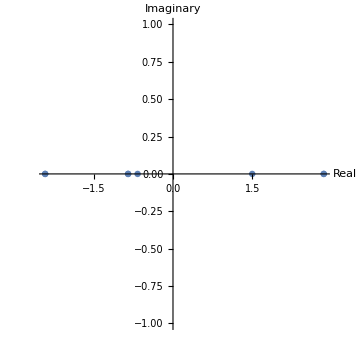

```mathematica
len=8
k=Range[0,len-1]
n=Range[0,len-1];
x2=Sin[3*Pi*n/len]
X2=Table[Sum[x2[[m+1]]*Exp[I*(-2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}];
Simplify[X2]
N[Simplify[X2]]
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[Simplify[X2]],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

```mathematica
N[Simplify[X1*X2]]
```

{5.98642,2.84776-6.8751 ⅈ,0.,-0.847759+0.351153 ⅈ,0.,-0.847759-0.351153 ⅈ,0.,2.84776+6.8751 ⅈ}

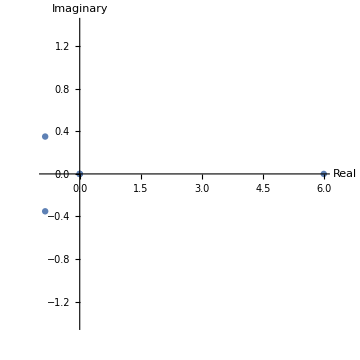

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[Simplify[X1*X2]],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

## Same thing as above but using the fourier version in Mathematica to verify

True

True

{5.98642+0. ⅈ,2.84776-6.8751 ⅈ,0.+0. ⅈ,-0.847759+0.351153 ⅈ,0.+0. ⅈ,-0.847759-0.351153 ⅈ,0.+0. ⅈ,2.84776+6.8751 ⅈ}

{1.2483,2.55487,2.55487,1.2483,0.248303,-1.05826,-1.05826,0.248303}

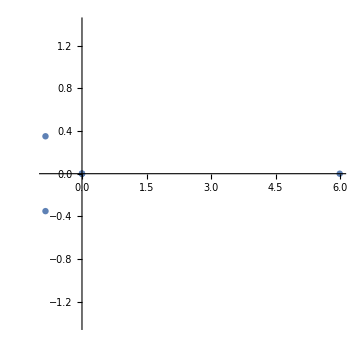

```mathematica
len=8; 
n=Range[0,len-1];
x1={1,1,1,1,0,0,0,0}; 
x2=Sin[3*Pi*n/len]; 

X11=Fourier[x1,FourierParameters->{1,-1}];
X22=Fourier[x2,FourierParameters->{1,-1}];
X1 == X11 (*This is to check against mine*)
X2 == X22
Y=X11*X22
y=InverseFourier[Y,FourierParameters->{1,-1}]; 
y=Simplify[y]
Show[Show[ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[Simplify[X11*X22]],AspectRatio->1],AxesStyle->Gray],ImageSize->Medium]
```

# #3 - 7.4 a and b

## a)

8

{0,1,2,3,4,5,6,7}

{1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2)}

{0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2)}

{0,4,0,0,0,0,0,4}

{0.,4.,0.,0.,0.,0.,0.,4.}

{0,-4 ⅈ,0,0,0,0,0,4 ⅈ}

{0.,0.-4. ⅈ,0.,0.,0.,0.,0.,0.+4. ⅈ}

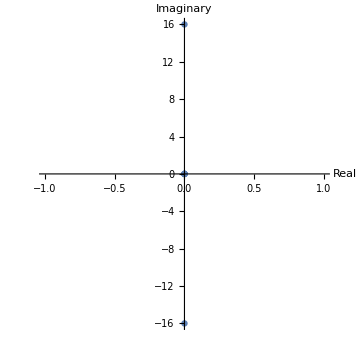

```mathematica
len=8
k=Range[0,len-1]
n=Range[0,len-1];
x1=Cos[2*Pi*n/len]
x2=Sin[2*Pi*n/len]
X1=Table[Sum[x1[[m+1]]*Exp[I*(-2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}];
Simplify[X1]
N[Simplify[X1]]

X2=Table[Sum[x2[[m+1]]*Exp[I*(-2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}];
Simplify[X2]
N[Simplify[X2]]
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[Simplify[X1*X2]],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

## b)

8

{0,1,2,3,4,5,6,7}

{1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2)}

{0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2)}

{0,-4 ⅈ,0,0,0,0,0,4 ⅈ}

{0,4 ⅈ,0,0,0,0,0,-4 ⅈ}

{0,16 ⅈ,0,0,0,0,0,-16 ⅈ}

{0,1/8 (-16 ⅈ ⅇ^(-(ⅈ π)/4)+16 ⅈ ⅇ^((ⅈ π)/4)),-4,1/8 (-16 ⅈ ⅇ^(-(3 ⅈ π)/4)+16 ⅈ ⅇ^((3 ⅈ π)/4)),0,1/8 (16 ⅈ ⅇ^(-(3 ⅈ π)/4)-16 ⅈ ⅇ^((3 ⅈ π)/4)),4,1/8 (16 ⅈ ⅇ^(-(ⅈ π)/4)-16 ⅈ ⅇ^((ⅈ π)/4))}

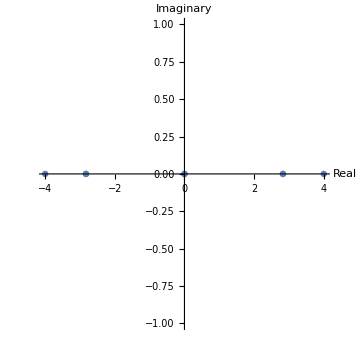

```mathematica
len=8
k=Range[0,len-1]
n=Range[0,len-1];
x1=Cos[2*Pi*n/len]
x2=Sin[2*Pi*n/len]
X1=Table[Sum[x1[[m+1]]*Exp[I*(-2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}];
Simplify[X1];
N[Simplify[X1]];

X2=Table[Sum[x2[[m+1]]*Exp[I*(-2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}];
X2 =Simplify[X2]
X2 = Conjugate[X2]
X3 =Simplify[X1*X2]
convRes=1/len * Table[Sum[X3[[m+1]]*Exp[I*(2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}](*inverse is just the same with pos j and div / len*)
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[convRes],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

## Same thing as above but using the fourier version in Mathematica to verify

```mathematica
(*verification*)
len=8; (*This should be the length of x1 and x2*)
n=Range[0,len-1];
x1=Sin[2*Pi*n/len]; (*Your first signal*)
x2=Sin[2*Pi*n/len]; (*Your second signal,could be any other function*)

X1=Fourier[x1,FourierParameters->{1,-1}]
X2=Conjugate[Fourier[x2,FourierParameters->{1,-1}]]
R=X1*X2 (*Pointwise multiplication*)
r=InverseFourier[R,FourierParameters->{1,-1}] (*Inverse DFT to get the circular correlation*)

r=Simplify[r]
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[r],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

{0.+0. ⅈ,0.-4. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+4. ⅈ}

{0.+0. ⅈ,0.+4. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-4. ⅈ}

{0.+0. ⅈ,16.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,16.+0. ⅈ}

{4.,2.82843,0.,-2.82843,-4.,-2.82843,0.,2.82843}

{4.,2.82843,0.,-2.82843,-4.,-2.82843,0.,2.82843}

-Graphics-

# #5 - 7.8

```mathematica
x1 = {1,2,3,1}
x2 = {4,3,2,2}
```

{1,2,3,1}

{4,3,2,2}

```mathematica
len=Length[x1]
k=Range[0,len-1]
n=Range[0,len-1]
```

4

{0,1,2,3}

{0,1,2,3}

```mathematica
X1=Table[Sum[x1[[m+1]]*Exp[I*(-2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}]
X2=Table[Sum[x2[[m+1]]*Exp[I*(-2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}]
X3 = X2*X1
```

{7,-2-ⅈ,1,-2+ⅈ}

{11,2-ⅈ,1,2+ⅈ}

{77,-5,1,-5}

{17,19,22,19}

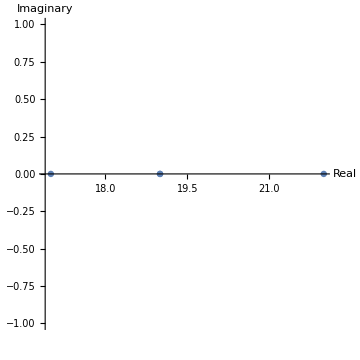

```mathematica
circConv = 1/len * Table[Sum[X3[[m+1]]*Exp[I*(2*Pi*k[[j+1]]*m/len)],{m,0,len-1}],{j,0,len-1}](*inverse is just the same with pos j and div / len*)
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[circConv],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

## Same thing as above but using the fourier version in Mathematica to verify

```mathematica
(*verification*)
x1 = {1,2,3,1}
x2 = {4,3,2,2}
len=Length[x1]; (*This should be the length of x1 and x2*)
n=Range[0,len-1];

X1=Fourier[x1,FourierParameters->{1,-1}]
X2=Fourier[x2,FourierParameters->{1,-1}]
R=X1*X2 (*Pointwise multiplication*)
r=InverseFourier[R,FourierParameters->{1,-1}] (*Inverse DFT to get the circular correlation*)

r=Simplify[r]
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[r],AspectRatio->1,AxesLabel->{"Real","Imaginary"},AxesStyle->Gray,ImageSize->Medium]
```

{1,2,3,1}

{4,3,2,2}

{7.+0. ⅈ,-2.-1. ⅈ,1.+0. ⅈ,-2.+1. ⅈ}

{11.+0. ⅈ,2.-1. ⅈ,1.+0. ⅈ,2.+1. ⅈ}

{77.+0. ⅈ,-5.+0. ⅈ,1.+0. ⅈ,-5.+0. ⅈ}

{17.,19.,22.,19.}

{17.,19.,22.,19.}

-Graphics-